# The Walking Dead

## Functions

```mathematica
SetDirectory[NotebookDirectory[]]
<<PajaroLocoPublic`
nonMigratoryForce=1000;
CalculateEuclideanDistances[coordinates_]:=Table[N[EuclideanDistance[coordinates[[i]],#]]&/@coordinates,{i,1,coordinates//Length }]
CalculateMigrationProbabilities[distancesMatrix_,nonMigratoryForce_]:=N[(#/Total[#])]&/@ReplaceAll[1/distancesMatrix//Quiet,ComplexInfinity->nonMigratoryForce]
ListPlotPoints[points_]:=ListPlot[points,
Frame->True,
Axes->True,
FrameStyle->Thickness[.005],
ImageSize->800,
FrameTicksStyle->None,
PlotStyle->PointSize[.025],
AspectRatio->1
]Options[EdgesStyleList2]:={LineThickness->.004,VariableStyle->"Both"}
EdgesStyleList2[vertexSyllableList_,OptionsPattern[]]:=Switch[OptionValue[VariableStyle],
"LineColor",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[1*vertexSyllableList[[i]][[2]]+.025],Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],
"LineWidth",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[.5],Blue,Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],
"Both",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[.75*vertexSyllableList[[i]][[2]]+.05],Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],_,Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}]]
edgeshape[e_,___]:={Arrowheads[{{.0075,.5}}],Arrow[e]}
Options[GraphTransitionsFrequenciesWithMax]:={ImagePadding->None,Background->White,VertexStyle->Automatic,VertexCoordinates->Automatic,LineThickness->.0005,VariableStyle->"Both",GraphLayout->Automatic,Frame->False,FrameStyle->Thick,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgeshape,VertexLabelStyle->{Italic},Prolog->{},Epilog->{},VertexShape->Automatic}
GraphTransitionsFrequenciesWithMax[frequenciesOutput_,max_,OptionsPattern[]]:=Module[{frequencies,syllables,edges,fixedEdgesList,vertexSyllableList,normalizedVertexSyllableList,edgesStyleList,links},frequencies=frequenciesOutput[[1]];
syllables=frequenciesOutput[[2]];
edges=Table[DirectedEdge[i,j]->frequencies[[i,j]],{i,Length[syllables]},{j,Length[syllables]}]//Flatten;
fixedEdgesList=DeleteCases[edges,DirectedEdge[_,_]->0];
vertexSyllableList=VertexNumberToVertexSyllable[frequenciesOutput[[2]],fixedEdgesList];
normalizedVertexSyllableList=(DirectedEdge[#[[1]],#[[2]][[1]]]->#[[2]][[2]]/max&)/@vertexSyllableList;
edgesStyleList=EdgesStyleList2[normalizedVertexSyllableList,LineThickness->OptionValue[LineThickness],VariableStyle->OptionValue[VariableStyle]];
links=DirectedEdge[#[[1]],#[[2,1]]]&/@vertexSyllableList;
Graph[syllables,links,
EdgeWeight->vertexSyllableList[[All,2,2]],
VertexStyle->OptionValue[VertexStyle],
EdgeStyle->edgesStyleList,
VertexCoordinates->OptionValue[VertexCoordinates],
ImageSize->OptionValue[ImageSize],
GraphLayout->OptionValue[GraphLayout],
EdgeShapeFunction->OptionValue[EdgeShapeFunction],
VertexShape->OptionValue[VertexShape],
VertexSize->OptionValue[VertexSize],
Frame->OptionValue[Frame],
FrameStyle->OptionValue[FrameStyle],
VertexLabelStyle->OptionValue[VertexLabelStyle],
VertexLabels->Placed["Name",Center],
EdgeLabels->Table[links[[i]]->Placed[fixedEdgesList[[All,2]][[i]],Tooltip],{i,Length[links]}],
Prolog->OptionValue[Prolog],
Epilog->OptionValue[Epilog],
Background->OptionValue[Background],
ImagePadding->OptionValue[ImagePadding],
PerformanceGoal->"Speed"
]
]
Themes`AddThemeRules["RandomPointsPlot",
AspectRatio->1,
Frame->True,
FrameLabel->(Style[#,20]&/@{"x (meters)","y (meters)"}),
FrameTicksStyle->20,
FrameStyle->Thick,
FrameTicks->{{None,All},{None,All}},
PlotStyle->Directive[PointSize[.02],Opacity[.75]],
AxesStyle->Directive[{Opacity[.25],Thick,Gray}]
]
Themes`AddThemeRules["RandomPointsMatrix",
AspectRatio->1,
Frame->True,
FrameStyle->Thick,
FrameTicks->{{None,None},{None,None}},
ColorFunction->"LakeColors",
AxesStyle->Directive[{Opacity[.25],Thick,Gray}]
]
DistributionIntoKernel[distribution_,center_,n_]:=Table[center+{Re[#],Im[#]}&[RandomReal[distribution] ⅇ^(ⅈ RandomReal[{0,2π}])],{n}]
MapDistributionParametersOnPoints[distribution_,centers_,n_]:=Join@@(DistributionIntoKernel[distribution,#,n]&/@centers)
SphereDistance[{ϕ1_,θ1_},{ϕ2_,θ2_},r_]:=r InverseHaversine[Haversine[ϕ1-ϕ2]+Cos[ϕ1]Cos[ϕ2]Haversine[θ1-θ2]]
SphereDistanceBetweenPoints[sphericalCoordinates1_,sphericalCoordinates2_]:=Module[{tuple},
tuple={
CoordinateTransformData["Cartesian"->"Spherical", "Mapping",sphericalCoordinates1],
CoordinateTransformData["Cartesian"->"Spherical", "Mapping",sphericalCoordinates2]
};
SphereDistance[{tuple[[1,2]],tuple[[1,3]]},{tuple[[2,2]],tuple[[2,3]]},tuple[[1,1]]]
]
SmoothHistogramPlot[sampledCoordinatesLayer_,{imageSize_,imagePadding_},plotRange_]:=SmoothHistogram[sampledCoordinatesLayer,
PlotStyle->Directive[{Thickness[.01],Opacity[.5]}],
ImageSize->imageSize,
PlotRange->{plotRange[[1]],plotRange[[2]]},
AspectRatio->.075,
Axes->False,
FrameTicks->{None,None},
Filling->Bottom,
FrameLabel->None,
ImagePadding->imagePadding,
ImageSize->imageSize,
PlotTheme->"RandomPointsPlot"
]
ListPlotScatter[clusteredCoordinates_,{imageSize_,imagePadding_},plotRange_]:=
ListPlot[clusteredCoordinates,
FrameTicks->Automatic,
BaseStyle->15,
LabelStyle->Directive[10],
FrameLabel->{{None,Rotate["y [meters]",180Degree]},{None,"x [meters]"}},
PlotRange->{plotRange[[1]],plotRange[[1]]},
PlotTheme->"RandomPointsPlot",
PlotStyle->Directive[{PointSize[.025],Opacity[.5]}],
ImageSize->imageSize,
ImagePadding->imagePadding
]
GenerateAccumulatedCoordinates[coordinatesRange_,citiesNumber_]:=Module[{sampledCoordinates,citiesDummy,names,pops,cities},
(*Generate Random Coordinates*)
sampledCoordinates=citiesDummy = Accumulate[RandomReal[{-coordinatesRange,coordinatesRange}, {citiesNumber, 2}]];
names = ToString /@ Range[citiesDummy // Length];
pops = RandomInteger[1000, citiesDummy // Length];
cities = Transpose[{names, citiesDummy, pops}];
{sampledCoordinates,names,pops,cities}
]
SyllableToID[a_,labels_]:=Position[labels,a]
ConvertSyllablesToID[sample_,syllablesLabels_]:=Table[SyllableToID[sample[[i]],syllablesLabels],{i,1,Length[sample]}]//Flatten
InTuples[communitiesList_,syllablesLabels_]:=Module[{communitiesIndexes},communitiesIndexes=Map[(Map[Position[syllablesLabels,#]&,#]//Flatten)&,communitiesList];
Tuples[#,2]&/@communitiesIndexes]
ListPlotSong[sample_,syllablesLabels_,OptionsPattern[]]:=Module[{texts,g},texts=Graphics[Text[Style[ToString[#[[1]]],OptionValue[TextSize]],{(sample//Length)+10,#[[2]]},Automatic],AspectRatio->1]&/@({syllablesLabels,Range[syllablesLabels//Length]}//Transpose);
g=ListPlot[
If[OptionValue[Labeling]==True,Labeled[#[[1]],#[[2]]]&,Tooltip[#[[1]],#[[2]]]&]/@({ConvertSyllablesToID[sample,syllablesLabels],ToString/@sample}//Transpose),
ImageSize->OptionValue[ImageSize],
PlotStyle->Directive[Opacity[.75],PointSize[Medium]],
Filling->None,
AxesLabel->{"TimeStep","ID"},
PlotRange->{0,syllablesLabels//Length},
ImagePadding->50,
GridLines->Automatic,
GridLinesStyle->Directive[LightBlue],
Frame->True,
FrameStyle->Directive[Thick,Black],
FrameTicksStyle->20
];
Show[g,texts,PlotRange->{0,(syllablesLabels//Length)+1}]
]
CalculateInOutRatio[inOutList_]:=(inOutList[[1]]/(inOutList[[1]]+inOutList[[2]]))
ListPlotSongWithCommunities[sample_,communities_,colors_,OptionsPattern[]]:=Module[{frequencyOutput,inOutTotals,labels2,individualCommunitiesInOutRatios,texts,connectionsRules,connectionsWithLabels,rect,rectangles,listPlot,sortedCommunities,wrappers,communitiesIDs,wrappersID},
frequencyOutput=GetTransitionsFrequencies[sample];
inOutTotals=GetCommunitiesInOutTransitionsFrequencies[frequencyOutput,communities,CountLoops->OptionValue[CountLoops]];
labels2=communities//Flatten//DeleteDuplicates;
sortedCommunities=Table[SortBy[i,Position[labels2,#]&],{i,communities}];
wrappers={(#//First)&/@sortedCommunities,(#//Last)&/@sortedCommunities}//Transpose;
communitiesIDs=Table[Position[labels2,#]&/@i//Flatten,{i,sortedCommunities}];
wrappersID={(#//First)&/@communitiesIDs,(#//Last)&/@communitiesIDs}//Transpose;
connectionsRules=wrappersID;
connectionsWithLabels=(UndirectedEdge[labels2[[#[[1]]]],labels2[[#[[2]]]]])&/@connectionsRules;
rect=Rectangle[{0.5,#[[1]]},{(sample//Length)+.5,#[[2]]},RoundingRadius->0]&/@connectionsRules;
rectangles=Graphics[
{
EdgeForm[Directive[Dashing[RandomReal[{0,0}]],Thickness[RandomReal[{.00175,.00175}]],Opacity[.2],colors[[#[[3]]]]]],Opacity[.2],colors[[#[[3]]]],#[[1]]
}
,ImagePadding->500]&/@({rect,Table[i[[1]]/(labels2//Length),{i,wrappersID}],Range[wrappersID//Length]}//Transpose);
individualCommunitiesInOutRatios=CalculateInOutRatio[#]&/@(inOutTotals//Transpose);
texts=Graphics[Text[Style[ToString[PaddedForm[#[[1]],{4,4}]],Bold,OptionValue[TextSize]],{(sample//Length)/2,#[[2]]+.35},Automatic],AspectRatio->1]&/@({individualCommunitiesInOutRatios,connectionsRules[[All,1]]}//Transpose);
listPlot=ListPlotSong[sample,labels2,ImageSize->OptionValue[ImageSize],Labeling->OptionValue[Labeling],TextSize->OptionValue[TextSize]];
Show[{listPlot,rectangles,texts}//Flatten]
]
```

/Users/sanchez.hmsc/Documents/GitHub/MoNeT/Dev/HectorSanchez/WalkingDead

RandomPointsPlot

RandomPointsMatrix

## Inputs

```mathematica
{vertexSize,vertexLabelSize}={2,10};
(*Set the number of cities wanted, the x-y coordinates range to sample from, and the number of site types allowd*)
{citiesNumber,coordinatesRange,classesNumber}={50,100,4};
(*Assigns a class type to each point based on a random uniform distribution of probabilities and the number of types defined previously*)
(*Set a vector with the probabilities the walker has to stay in current node or move to the others. This vector is then rotated to generate the "partiteness" mask.*)
directionStrength=1;
movementProbabilitiesVector={0,1,0,0};
(*The penalizations matrix is a type-based transitions matrix to be used as mask down the road*)
penalizationsMatrix=Table[RotateRight[movementProbabilitiesVector,i-1],{i,1,classesNumber}];
MatrixForm[penalizationsMatrix]
```

(0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0)

## Generate Random Spatial Setting

{{1,2,3,4,6,8,9,10,11,13,14,15,16},{5,12},{7,17,19,25,26,27,28,29},{18,20,21,22,23,24},{30,35},{31},{32,33,38,41},{34},{36,37},{39,40},{42,43,47},{44,45,46,48,49},{50}}

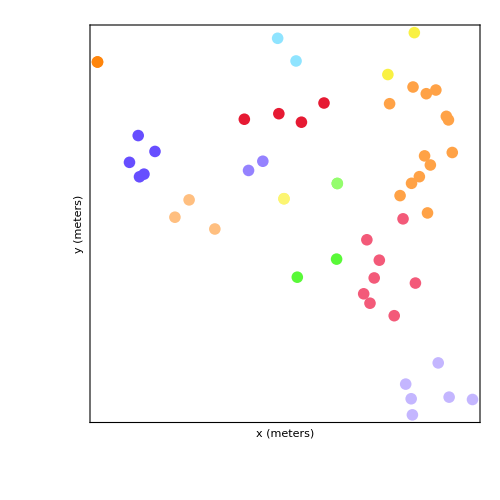

```mathematica
(*This is a very basic algorithm to generate points in a landscape. Replace it with a better later on.*)
{sampledCoordinates,names,pops,cities}=GenerateAccumulatedCoordinates[-100,citiesNumber];
distances = CalculateEuclideanDistances[sampledCoordinates];
(*Geo-Clustering*)
clusteredCoordinates=FindClusters[sampledCoordinates,Method->"NeighborhoodContraction"];
clustersStrings=Table[ToString/@Flatten[Position[cities[[All,2]],#]&/@clusteredCoordinates[[i]]],{i,1,clusteredCoordinates//Length}]
clustersIDs=Position[Map[ToExpression,clustersStrings,Infinity],#][[1,1]]&/@Range[Length[sampledCoordinates]];
(*Plots*)
colors=Reverse[ColorData["BrightBands",#]&/@Range[0,1,1/(Length[clustersStrings])]]//Flatten//RandomSample;
ListPlot[clusteredCoordinates,PlotTheme->"RandomPointsPlot",ImageSize->500,PlotStyle->colors]
```

## Analyze

Map

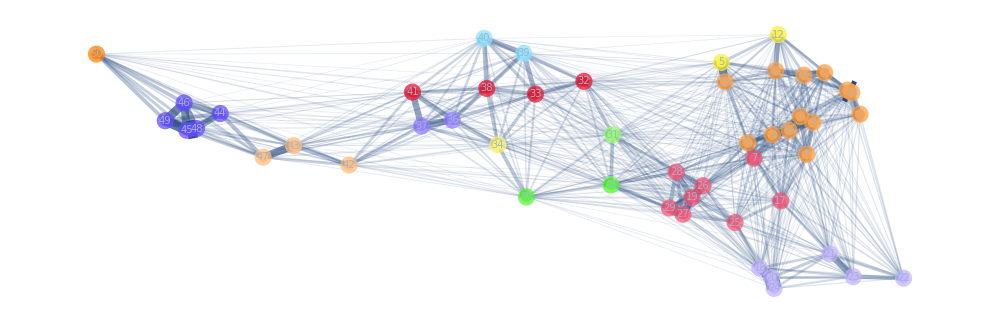

```mathematica
(*This "migration" is replacing the real kernel for the time being. It is based on the inverse of the distance to other nodes.*)
migration = CalculateMigrationProbabilities[distances, .05];
edgeshape2[e_,___]:={Arrowheads[{{.000001,.9}}],Arrow[e]}
stylesSwatch=Directive[Opacity[1],colors[[#]],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[clusteredCoordinates//Length];
stylesList=(ToString[#[[1]]]->stylesSwatch[[#[[2]]]])&/@Transpose[{Range[clustersIDs//Length],clustersIDs}];
map = GraphTransitionsFrequenciesWithMax[
  {
Chop[ReplacePart[migration,{i_,i_}->0]//LowerTriangularize,10^-2],
ToString /@ Range[Length[migration]]
   }, .15,
 VertexStyle ->stylesList,
VertexCoordinates ->sampledCoordinates,
VertexSize ->1vertexSize,
VertexLabelStyle->vertexLabelSize,
ImageSize -> 1000,
LineThickness -> .0075,
EdgeShapeFunction->edgeshape2,
VariableStyle->"Both"
  ]
```

```mathematica
Export["00_clustering.pdf",map,ImageSize->2000,ImageResolution->500]
```

00_clustering.pdf

Mask Movement with Site-Types

```mathematica
(*If the transition between city types is not possible, or improbable, then mask it with the corresponding value. After that, normalize for the probabilities to still add up to one.*)
cityType=RandomChoice[Range[classesNumber],sampledCoordinates//Length]
{cityType[[1]],#}&/@cityType;
```

{4,1,2,1,2,3,2,2,2,1,4,4,1,4,4,3,4,1,3,3,1,2,3,3,3,2,3,2,4,4,2,4,3,1,4,1,4,1,4,3,1,1,1,3,3,3,2,4,4,3,3,3,2,3,1,4,3,3,4,3,2,2,2,2,2,3,2,1,1,2,4,2,4,2,2,4,1,4,2,2,4,1,3,1,1,3,3,1,3,4,4,1,4,3,4,4,1,3,1,1,4,1,3,1,2,1,1,4,3,4,1,4,3,4,1,1,4,2,2,2,4,3,2,1,1,1,2,3,2,3,1,2}

```mathematica
penalizationsMask=Table[penalizationsMatrix[[i,#]]&/@cityType,{i,cityType}];
normalizedMaskedMatrix=(#/Total[#])&/@(penalizationsMask*migration);
(*Plots*)
penalizationsMaskPlot=penalizationsMask//MatrixPlot[#,ColorFunction -> "LakeColors", ImageSize ->500/2]&;
colorsType=Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/classesNumber]];
stylesSwatchType=Directive[Opacity[1],colorsType[[#]],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[classesNumber];
stylesListType=(ToString[#[[1]]]->stylesSwatchType[[#[[2]]]])&/@Transpose[{Range[cityType//Length],cityType}];
normalizedMaskedMatrixPlot=normalizedMaskedMatrix//MatrixPlot[#,ColorFunction->"LakeColors"]&;
```

Movement Network

```mathematica
edgeshape2[e_,___]:={Arrowheads[{{.01,.75}}],Arrow[e]}
graph = GraphTransitionsFrequenciesWithMax[
  {
Chop[normalizedMaskedMatrix,10^-1.5],
ToString /@ Range[Length[normalizedMaskedMatrix]]
   }, .5,
 VertexStyle->stylesListType,
VertexCoordinates->sampledCoordinates,
VertexSize ->vertexSize,
VertexLabelStyle->vertexLabelSize,
ImageSize->1000,
LineThickness->.005,
EdgeShapeFunction->edgeshape2,
VariableStyle->"Both"
  ]
Export["01_Movement.pdf",%,ImageSize->2000,ImageResolution->500]
```

-Graphics-

01_Movement.pdf

Sink and Source

```mathematica
differenceThreshold=.3;
(**)
communities=Map[ToExpression,clustersStrings,Infinity]
outCommunity=Table[
comm=communities[[i]];
transitions=ReplacePart[normalizedMaskedMatrix,{i_,i_}->0];
Total[Total/@(Delete[transitions[[comm]]//Transpose,{#}&/@comm]//Transpose)]
,{i,1,Length[communities]}];
inCommunity=Table[
comm=communities[[i]];
transitions=ReplacePart[normalizedMaskedMatrix,{i_,i_}->0]//Transpose;
Total[Total/@(Delete[transitions[[comm]]//Transpose,{#}&/@comm]//Transpose)]
,{i,1,Length[communities]}];
outMinusIn=outCommunity-inCommunity;
typeOfCommunity=If[Abs[#]<differenceThreshold,"Bridge",If[#>0,"Source","Sink"]]&/@outMinusIn
(**)
gridSourceSink=Grid[{
Style[PaddedForm[#,{3,3}],7.5,Bold]&/@outMinusIn,
Style[#,7.5,Bold]&/@typeOfCommunity
},
Frame->True,Background->{Lighter[#,0.1]&/@colors[[1;;Length[outMinusIn]]],None},ItemSize->3]
edges=Table[colors[[i]]&/@clustersStrings[[i]],{i,1,Length[clustersStrings]}]//Flatten;
flattenedRatios=Table[ConstantArray[typeOfCommunity[[i]],communities[[i]]//Length],{i,1,communities//Length}]//Flatten;
graphSinkSource=HighlightGraph[graph, Style[#[[2]] ,Directive[EdgeForm[Directive[Opacity[1],Switch[#[[3]],"Bridge",Black,"Sink",Darker[Blue,0],"Source",Darker[Red,0]],Thickness[.005]]],#[[1]]]] & /@ ({edges,clustersStrings//Flatten,flattenedRatios} // Transpose)];
```

{{1,2,3,4,5,13,14,15,16,17,25,26,27,28,29,37,38,39,40,50,51,52},{6,7,6,7,8,9,10,11,12,18,19,18,19,20,21,22,23,24,32,33,34,35,36,45,46,47,48,57,58,59},{30,31,30,31,41,42,43,42,43,44,53,54,55,54,55,56,65,66,67,66,67,68,77,78,79,78,79,80,89,90,91,90,91,92,102,103,102,103},{49,61,62,63,64,73},{60,69,70,71,72,84},{74,75,76,85,86,87,88,97,98,99,100,101,109,110,111,112,113,114,115,114,115,121,122,123,124,125,126,127,126,127},{81,82,83,93,94,95,96,104,105,106,107,108,116,117,118,119,120,128,129,130,131,132}}

{Bridge,Source,Sink,Bridge,Bridge,Source,Source}

0.136 |  1.090 | -5.870 |  0.011 | -0.089 |  2.420 |  0.674
Bridge | Source | Sink | Bridge | Bridge | Source | Source

Sinks and Sources Report

```mathematica
gridSinksAndSources=Grid[{
Style[#,25]&/@{"Clustered Map","","Point Types","","Sources (R) and Sinks(B)"},
{map,Style["+",Bold,50],graph,Style["=",Bold,50],Grid[{{graphSinkSource},{gridSourceSink}}]}
}]
Export["02_grid.pdf",%]
```

Clustered Map |  | Point Types |  | Sources (R) and Sinks(B)
-Graphics- | + | -Graphics- | = | -Graphics-
 0.136 |  1.090 | -5.870 |  0.011 | -0.089 |  2.420 |  0.674
Bridge | Source | Sink | Bridge | Bridge | Source | Source

02_grid.pdf

Centrality Analysis

```mathematica
BetweennessCentrality[map]
a=HighlightGraph[map,VertexList[map],VertexSize-> Thread[VertexList[map]-> Rescale[%]]];
BetweennessCentrality[graph]
b=HighlightGraph[graph,VertexList[graph],VertexSize-> Thread[VertexList[graph]-> Rescale[%]]];
Grid[{{a,b}}]
```

{0.,1.49419,10.5807,32.7163,25.3131,27.8714,27.8714,25.6399,16.2157,10.2733,10.2733,2.21294,3.06599,11.5381,27.1794,75.4713,66.7822,47.8943,47.8943,68.0674,63.1674,40.4618,17.6398,5.07066,19.5667,44.7735,84.4523,193.624,174.197,125.22,125.22,165.387,189.719,96.386,52.3938,23.6936,57.8788,151.712,117.243,161.292,233.361,159.588,159.588,236.139,154.746,98.7767,155.482,62.8799,66.4996,76.9451,179.373,201.811,290.548,167.622,167.622,296.626,193.562,159.91,78.8449,63.5972,74.8645,62.8552,202.119,208.733,269.501,191.936,191.936,275.045,203.738,180.22,61.3853,73.5852,52.9162,138.381,164.901,186.199,217.341,202.128,202.128,221.81,182.507,146.89,131.824,52.757,42.5596,92.024,126.279,192.413,238.326,154.361,154.361,229.589,178.68,93.9336,75.9355,38.5398,8.69142,30.6335,59.2424,132.727,96.2792,88.0947,88.0947,83.2935,97.1953,44.0976,22.9461,7.63462,11.3553,11.2785,50.4196,63.9972,80.1505,32.7092,32.7092,63.8935,45.1016,37.89,9.32078,6.49043,3.00846,4.81879,20.9414,21.4051,17.8624,27.306,27.306,25.0524,6.67232,2.68597,1.01812,0.}

{41.1909,315.099,142.293,334.344,215.951,176.566,380.728,294.09,290.11,188.737,89.9283,79.3228,291.82,199.327,315.642,208.79,492.754,430.528,134.161,107.495,342.457,232.803,135.261,69.8073,109.974,87.8526,360.419,311.751,491.694,500.685,805.279,677.446,322.755,438.388,195.043,211.569,225.751,440.078,526.919,618.412,495.868,424.614,424.614,532.654,508.132,187.786,281.739,273.897,424.37,200.658,489.953,914.569,406.857,579.933,611.785,540.026,489.106,430.505,688.749,159.626,296.399,266.638,467.92,597.984,571.106,606.848,782.743,427.708,638.814,548.79,424.119,256.676,312.792,270.5,371.403,390.012,312.671,648.842,885.99,817.868,525.655,400.666,376.081,183.109,116.347,327.192,632.447,525.638,514.621,441.978,441.978,349.471,404.821,618.146,186.002,113.323,110.362,217.964,286.51,558.879,623.362,496.955,476.736,346.005,533.957,302.997,235.29,126.124,59.8405,187.649,164.16,383.709,369.267,285.658,218.8,262.463,217.336,249.161,240.843,173.166,162.894,58.2044,353.568,145.161,107.72,187.143,420.085,316.101,224.755,328.989,50.2348,121.994}

-Graphics-

```mathematica
ClosenessCentrality[map]
a=HighlightGraph[map,VertexList[map],VertexSize-> Thread[VertexList[map]-> Rescale[%]]];
ClosenessCentrality[graph]
b=HighlightGraph[graph,VertexList[graph],VertexSize-> Thread[VertexList[graph]-> Rescale[%]]];
Grid[{{a,b}}]
```

{0.,24.9189,35.7255,46.2372,41.1935,39.678,39.678,38.9133,37.1331,34.9447,40.3934,33.8191,47.6998,44.454,53.7668,49.9363,39.36,39.0532,39.0532,34.0242,38.0014,39.8287,31.5705,31.3787,49.8177,45.0333,49.285,49.046,43.783,40.2501,40.2501,37.0433,36.9684,39.1555,33.3257,31.3409,46.6163,44.4121,43.7978,38.8966,40.6304,38.9547,38.9547,37.9674,34.222,31.5156,35.3922,31.5198,34.2761,37.696,39.8159,37.3809,39.9017,36.3502,36.3502,37.9624,34.4438,32.3161,33.567,29.7942,32.1494,33.214,37.143,33.8792,36.8246,35.1752,35.1752,35.5874,32.4262,32.068,32.0541,29.128,30.3158,31.7674,34.2431,32.3043,34.5031,33.6542,33.6542,33.7862,31.2172,30.9468,31.5834,28.6623,31.4896,32.2773,31.6974,30.27,31.7217,30.8416,30.8416,31.3293,29.5974,29.4503,31.7112,28.9365,29.598,30.2913,30.6803,31.4215,29.3314,28.8572,28.8572,29.0214,30.3951,30.8299,29.9591,27.8325,28.3605,28.1326,30.2107,30.2964,29.4474,29.064,29.064,29.0817,30.8825,30.6348,28.1107,29.1261,30.03,28.0469,30.1294,29.858,30.8291,31.678,31.678,31.1348,30.195,30.7236,30.9383,30.7907}

{5.96058,7.96861,7.28445,7.30349,7.45413,7.32294,7.77556,7.2685,7.67247,7.10478,6.18805,7.63475,7.95857,7.14297,7.67597,6.96159,7.54426,7.28707,7.02627,6.66928,6.88228,7.56607,6.8735,6.88716,7.13033,6.62957,6.85323,7.45485,7.31348,7.26023,8.46203,7.59782,7.81821,7.79929,6.66663,7.51026,7.25593,7.21397,7.72193,7.89918,8.36671,8.36539,8.36539,8.01895,8.16652,7.69794,7.08186,7.38851,7.75812,7.05578,7.90105,8.70861,7.30474,8.12587,8.37643,7.89394,7.79326,7.40971,8.47045,6.88406,7.427,7.68649,7.98748,7.71733,8.00458,8.32291,8.30322,8.15833,8.30143,8.09176,7.57787,7.34103,7.14243,7.58363,7.64226,7.50969,7.40135,7.87313,8.78834,7.87061,7.9865,7.73108,6.97658,6.98759,7.11591,8.30335,8.36853,8.25289,6.99882,7.58933,7.58933,7.71043,7.69301,8.02855,7.12679,7.30237,7.95527,7.51363,8.21229,8.31018,7.6785,8.23972,7.23424,7.8863,7.72978,8.09005,7.01412,7.71388,6.67548,6.75702,8.28327,6.9526,7.23295,7.38508,8.03655,7.95935,7.48342,6.75374,7.27211,7.54317,7.4447,6.843,7.28461,8.35369,7.63423,8.28452,7.89969,7.63791,6.8284,7.97865,6.88813,7.27448}

-Graphics-

Walkers

```mathematica
kernel=normalizedMaskedMatrix;
initialState=ConstantArray[0,kernel//Length]//ReplacePart[#,3->1]&;
markov=DiscreteMarkovProcess[initialState,kernel];
```

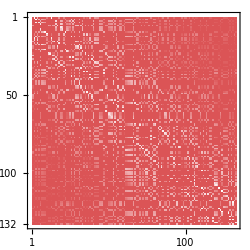
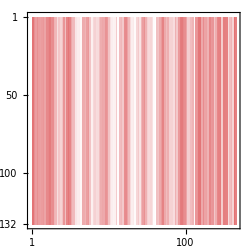
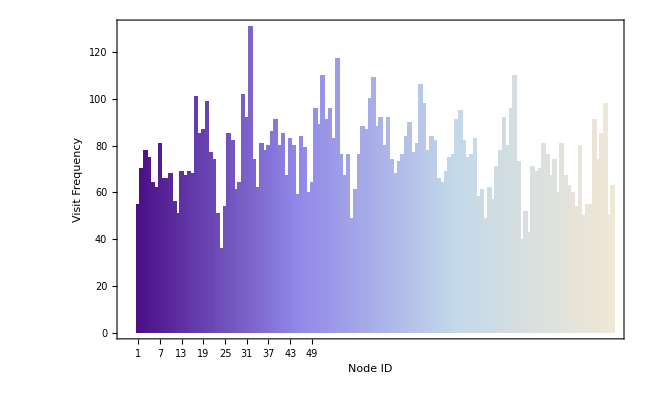
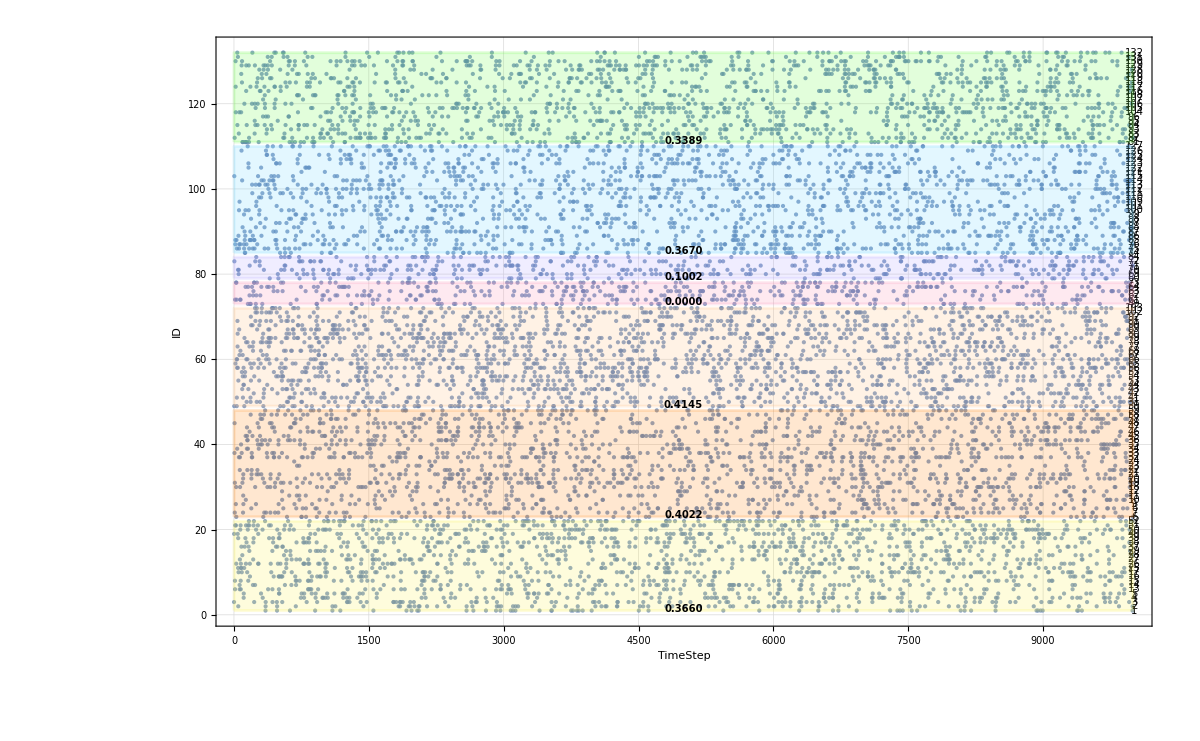
Transitions | Limiting
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
(**)
data=RandomFunction[markov,{0,10000}];
tally=(data//Normal)[[All,All,2]][[1]]//Tally//Sort;
barChartFrequency=BarChart[tally[[All,2]],
ChartStyle->"LakeColors",
ChartLabels->tally[[All,1]],
ImageSize->650,
Frame->True,
FrameStyle->Thick,
FrameTicksStyle->Directive[8],
FrameLabel->(Style[#,25]&/@{"Node ID","Visit Frequency"})
];
songs=ListPlotSongWithCommunities[(data//Normal)[[1,All,2]],Map[ToExpression,clustersStrings,Infinity],colors,ImageSize->1200,TextSize->10];
{Range[Length[kernel]],MarkovProcessProperties[markov,"HoldingTimeMean"]}//MatrixForm;
limitMatrix=MarkovProcessProperties[markov,"LimitTransitionMatrix"]//MatrixPlot[#,PlotLegends->Placed[Automatic,Below],ColorFunction->"CherryTones",ImageSize->250]&;
transitionsMatrix=MarkovProcessProperties[markov,"TransitionMatrix"]//MatrixPlot[#,PlotLegends->Placed[Automatic,Below],ColorFunction->"CherryTones",ImageSize->250]&;
matricesGrid=Grid[{Style[#,15]&/@{"Transitions","Limiting"},{transitionsMatrix,limitMatrix}}];
gridRandomWalker=Grid[{{Grid[{{matricesGrid},{barChartFrequency}}],songs}}]
```

Markov

```mathematica
MarkovProcessProperties[markov,"LimitTransitionMatrix"][[1]];
```

```mathematica
trans=Transpose[kernel];
{eVals,eVecs}=Eigensystem[trans]//N;
Normalize[eVecs[[1]],Total];
```

Normalize::nlnfa: The second argument Total is not a norm function that always returns a non-negative real number for any numeric argument.

{0.00488118,0.00658256,0.00697057,0.00658549,0.00695844,0.00702538,0.00694683,0.00683611,0.00713778,0.00623566,0.00612721,0.00555029,0.00656514,0.00647771,0.0075888,0.00772505,0.00881134,0.0081802,0.00843951,0.00804123,0.00680641,0.00796503,0.00607277,0.00503781,0.00600072,0.0072729,0.0077681,0.00778968,0.00913751,0.00962492,0.00954782,0.010258,0.0073532,0.00742183,0.00768084,0.00702183,0.00686208,0.00808992,0.00969983,0.00860924,0.00841474,0.00868928,0.00868928,0.00800116,0.0074458,0.00729027,0.00733787,0.00673993,0.00693419,0.00805287,0.00883082,0.00966258,0.00988196,0.00973753,0.00827316,0.0105584,0.00793277,0.00774026,0.00821691,0.00651339,0.00636418,0.00708396,0.00778645,0.00864733,0.00965962,0.00947658,0.0103923,0.00848175,0.00823459,0.00907857,0.00769917,0.00699823,0.00662016,0.00758015,0.00838576,0.00861798,0.00847322,0.00883778,0.0104214,0.0106314,0.00795945,0.00805647,0.00734658,0.00688452,0.00590665,0.00731739,0.00793054,0.00752525,0.00840334,0.00843692,0.00843692,0.0087068,0.0075663,0.00818745,0.0068742,0.00565835,0.00549672,0.00613735,0.00649083,0.00725478,0.00834874,0.00833527,0.00793056,0.00765036,0.0100861,0.00683479,0.00677953,0.00516361,0.00496408,0.00731685,0.0064229,0.00708756,0.00704601,0.0075922,0.00616364,0.00686602,0.00682179,0.00818715,0.00749863,0.00620158,0.00581292,0.00556582,0.0082754,0.00566962,0.00572149,0.00581929,0.00873008,0.00795521,0.00766306,0.00845861,0.00467002,0.00568371}

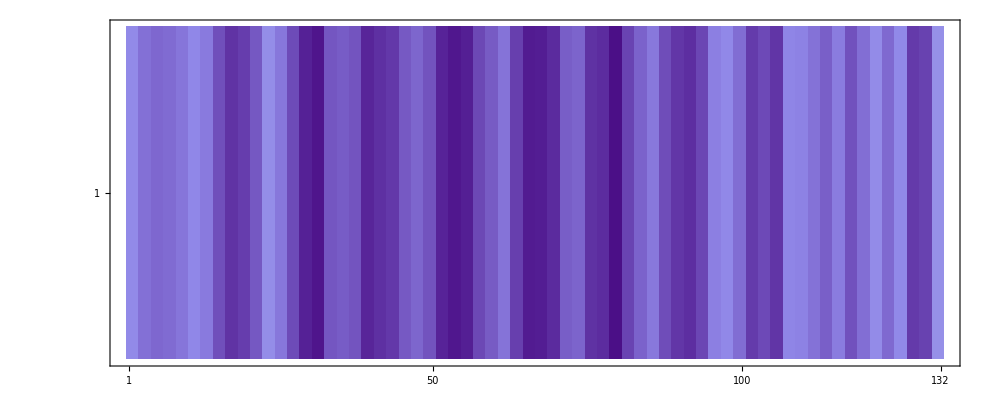

```mathematica
markov=DiscreteMarkovProcess[initialState,kernel];
markovPDF=PDF[StationaryDistribution[markov],#]&/@Range[markov[[1]]//Length]
MatrixPlot[{markovPDF},ColorFunction->ColorData[{"LakeColors","Reverse"}],ImageSize->1000]
(*MatrixPlot[{tally[[All,2]]},ColorFunction->ColorData[{"LakeColors","Reverse"}],ImageSize->1000]*)
```

```mathematica
{Range[markov[[1]]//Length],markovPDF}//Transpose
```

{{1,0.00488118},{2,0.00658256},{3,0.00697057},{4,0.00658549},{5,0.00695844},{6,0.00702538},{7,0.00694683},{8,0.00683611},{9,0.00713778},{10,0.00623566},{11,0.00612721},{12,0.00555029},{13,0.00656514},{14,0.00647771},{15,0.0075888},{16,0.00772505},{17,0.00881134},{18,0.0081802},{19,0.00843951},{20,0.00804123},{21,0.00680641},{22,0.00796503},{23,0.00607277},{24,0.00503781},{25,0.00600072},{26,0.0072729},{27,0.0077681},{28,0.00778968},{29,0.00913751},{30,0.00962492},{31,0.00954782},{32,0.010258},{33,0.0073532},{34,0.00742183},{35,0.00768084},{36,0.00702183},{37,0.00686208},{38,0.00808992},{39,0.00969983},{40,0.00860924},{41,0.00841474},{42,0.00868928},{43,0.00868928},{44,0.00800116},{45,0.0074458},{46,0.00729027},{47,0.00733787},{48,0.00673993},{49,0.00693419},{50,0.00805287},{51,0.00883082},{52,0.00966258},{53,0.00988196},{54,0.00973753},{55,0.00827316},{56,0.0105584},{57,0.00793277},{58,0.00774026},{59,0.00821691},{60,0.00651339},{61,0.00636418},{62,0.00708396},{63,0.00778645},{64,0.00864733},{65,0.00965962},{66,0.00947658},{67,0.0103923},{68,0.00848175},{69,0.00823459},{70,0.00907857},{71,0.00769917},{72,0.00699823},{73,0.00662016},{74,0.00758015},{75,0.00838576},{76,0.00861798},{77,0.00847322},{78,0.00883778},{79,0.0104214},{80,0.0106314},{81,0.00795945},{82,0.00805647},{83,0.00734658},{84,0.00688452},{85,0.00590665},{86,0.00731739},{87,0.00793054},{88,0.00752525},{89,0.00840334},{90,0.00843692},{91,0.00843692},{92,0.0087068},{93,0.0075663},{94,0.00818745},{95,0.0068742},{96,0.00565835},{97,0.00549672},{98,0.00613735},{99,0.00649083},{100,0.00725478},{101,0.00834874},{102,0.00833527},{103,0.00793056},{104,0.00765036},{105,0.0100861},{106,0.00683479},{107,0.00677953},{108,0.00516361},{109,0.00496408},{110,0.00731685},{111,0.0064229},{112,0.00708756},{113,0.00704601},{114,0.0075922},{115,0.00616364},{116,0.00686602},{117,0.00682179},{118,0.00818715},{119,0.00749863},{120,0.00620158},{121,0.00581292},{122,0.00556582},{123,0.0082754},{124,0.00566962},{125,0.00572149},{126,0.00581929},{127,0.00873008},{128,0.00795521},{129,0.00766306},{130,0.00845861},{131,0.00467002},{132,0.00568371}}

```mathematica
stylesSwatchType=Directive[Opacity[1],colorsType[[#]],EdgeForm[Directive[Opacity[.75],Thickness[.0025]]]]&/@Range[classesNumber];
stylesListType=(ToString[#[[1]]]->stylesSwatchType[[#[[2]]]])&/@Transpose[{Range[cityType//Length],cityType}];
edgeshape2[e_,___]:={Arrowheads[{{.0075,.8}}],Arrow[e]}
graph = GraphTransitionsFrequenciesWithMax[
  {
Chop[normalizedMaskedMatrix,10^-1.5],
ToString /@ Range[Length[normalizedMaskedMatrix]]
   }, .25,
 VertexStyle->stylesListType,
VertexCoordinates->sampledCoordinates,
VertexSize -> Thread[VertexList[graph]->10*Log[1.5+3*Rescale[markovPDF]]],
VertexLabelStyle->6.5,
ImageSize->1000,
LineThickness->.0005,
EdgeShapeFunction->edgeshape2,
VariableStyle->"Both"
  ]
Export["03_MarkovStationary.pdf",%]
```

-Graphics-

03_MarkovStationary.pdf

## Export Report

```mathematica
Grid[{{gridSinksAndSources},{gridRandomWalker}}]
Export["NetworkReport"<>StringPadLeft[ToString[(directionStrength*100)//Round],3,"0"]<>".pdf",%,ImageSize->5000,ImageResolution->500]
```